```mathematica
Map[First,Select[Table[With[{g=ReadGrof[k]},k->Select[VertexList[g],VertexDegree[g,#]==5&]],{k,100}],#[[2]]≠{}&]]
```

{3,5,6,7,9,10,11,12,13,14,15,16,17,18,19,20,24,25,26,27,28,29,30,31,33,34,35,36,37,38,39,40,41,42,43,44,46,47,48,49,50,51,53,54,56,57,58,59,60,61,63,64,65,66,67,68,70,71,74,75,76,77,78,79,80,81,83,84,85,86,87,88,89,90,91,92,93,94,96,97,98,99,100}

```mathematica
GraphWithChrom2[g_, divide_]:=Block[{chrom=ChromaticPolynomial[g,x],chrom4},
chrom4=chrom/.x->4;
Labeled[Graph[g,ImageSize->120],Style[{Factor[chrom/divide],chrom4/divide/.x->4,PlanarGraphQ[g]},If[chrom4!=0,Darker[Green],Red],If[PlanarGraphQ[g],Underlined,Bold],8]]
]
```

```mathematica
FormatChrom[l_List]:=Map[
Style[#,If[(#/.x->4)==0,Red,Darker[Green]]]&,l]
```

```mathematica
Exponent[x^3+3x,x]
```

3

```mathematica
WorkOnGraph3[g_Graph,vertices_List]:=Block[{split,left, right,left2,right2,middle2,middle,sols,lefta,middlea,righta,middleC},
split= ConnectedComponents[VertexDelete[g,vertices]];
left=VertexDelete[g,split[[1]]];
right=VertexDelete[g,split[[2]]];
middle=VertexDelete[g,Select[DeleteDuplicates[Join[VertexList[left],VertexList[right]]],!MemberQ[vertices,#]&]];
left2=MakeComplete[left,vertices];
right2=MakeComplete[right,vertices];
middle2=MakeComplete[middle,vertices];
sols=Map[SymbolToSets,FindFullFormula[middle]]//Reverse;
TableForm[
Table[
middlea=ApplyToGraph[middle2,sol];
lefta=Graph[ApplyToGraph[left2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
righta=Graph[ApplyToGraph[right2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
middleC=ChromaticPolynomial[middlea,x];
FormatChrom[Factor[Simplify[{ChromaticPolynomial[lefta,x]/middleC,ChromaticPolynomial[righta,x]/middleC,Exponent[middleC,x]}]]],
{sol,sols}
]
]
]
```

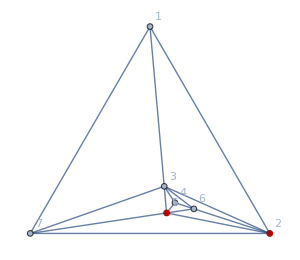

```mathematica
With [{g=ReadGrof[5]},
Graph[g,VertexLabels->"Name",GraphLayout->"TutteEmbedding", GraphHighlight->Select[VertexList[g],VertexDegree[g,#]==5&],ImageSize->300]
]
```

```mathematica
Block[{g=ReadGrof[5],vertices, adj},
vertices=Select[VertexList[g],VertexDegree[g,#]==5&];
Table[
adj=AdjacencyList[g,v];
v->WorkOnGraph3[g,adj]
,{v,vertices}
]
]
```

{2→-3+x | -3+x
-3+x | -4+x
-3+x | -4+x
-3+x | -4+x
-3+x | -5+x,5→-3+x | -3+x
-4+x | -3+x
-4+x | -3+x
-4+x | -3+x
-5+x | -3+x}

```mathematica
Block[{g=ReadGrof[2345],vertices, adj},
vertices=Select[VertexList[g],VertexDegree[g,#]==5&];
Table[
adj=AdjacencyList[g,v];
v->Labeled[Framed[WorkOnGraph3[g,adj]],adj]
,{v,vertices}
]
]
```

{2→-4+x | (-3+x)^6
-3+x | (-3+x)^6
-4+x | (-3+x)^6
-4+x | (-3+x)^6
-5+x | (-3+x)^6{1,3,7,9,11},9→(-3+x)^3 | (-3+x)^5
(-4+x) (-3+x)^2 | (-4+x) (-3+x)^4
(-4+x) (-3+x)^2 | (-4+x) (-3+x)^4
(-4+x) (-3+x)^2 | (-4+x) (-3+x)^4
(-5+x) (-3+x)^2 | (-5+x) (-3+x)^4{2,3,11,5,6},11→(-3+x)^2 | (-3+x)^6
12-7 x+x^2 | (-3+x)^6
12-7 x+x^2 | (-3+x)^6
12-7 x+x^2 | (-3+x)^6
15-8 x+x^2 | (-3+x)^6{2,3,7,9,5},5→(-3+x)^4 | (-3+x)^4
(-4+x) (-3+x)^3 | (-4+x) (-3+x)^3
(-4+x) (-3+x)^3 | (-4+x) (-3+x)^3
(-4+x) (-3+x)^3 | (-4+x) (-3+x)^3
(-5+x) (-3+x)^3 | (-5+x) (-3+x)^3{3,9,11,6,12},8→-4+x | (-3+x)^6
-3+x | (-3+x)^6
-4+x | (-3+x)^6
-4+x | (-3+x)^6
-5+x | (-3+x)^6{3,6,12,4,10},12→(-3+x)^2 | (-3+x)^6
12-7 x+x^2 | (-4+x) (-3+x)^5
12-7 x+x^2 | (-4+x) (-3+x)^5
12-7 x+x^2 | (-4+x) (-3+x)^5
15-8 x+x^2 | (-5+x) (-3+x)^5{3,5,6,8,10}}

```mathematica
WorkOnGraph3[ReadGrof[5],{1,3,7,5,6}]
```

-3+x | -3+x
-3+x | -4+x
-3+x | -4+x
-3+x | -4+x
-3+x | -5+x

```mathematica
WorkOnGraph3[ReadGrof[5],{1,3,6,5,7}]
```

-3+x | -3+x
-3+x | -4+x
-3+x | -4+x
-3+x | -4+x
-3+x | -5+x

```mathematica
WorkOnGraph3[ReadGrof[5],{7,3,4,6,2}]
```

-3+x | -3+x
-4+x | -3+x
-4+x | -3+x
-4+x | -3+x
-5+x | -3+x

```mathematica
WorkOnGraph3[ReadGrof[5],{1,3,6,5,7}]
```

-3+x | -3+x
-3+x | -4+x
-3+x | -4+x
-3+x | -4+x
-3+x | -5+x

```mathematica
WorkOnGraph3[ReadGrof[5],Reverse[{1,3,6,5,7}]]
```

-3+x | -3+x
-3+x | -4+x
-3+x | -4+x
-3+x | -4+x
-3+x | -5+x

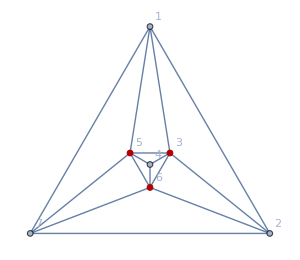

```mathematica
With [{g=ReadGrof[6]},
Graph[g,VertexLabels->"Name",GraphLayout->"TutteEmbedding", GraphHighlight->Select[VertexList[g],VertexDegree[g,#]==5&],ImageSize->300]
]
```

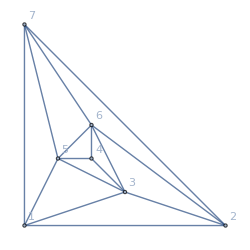
-Graphics-{(-3+x) (-2+x) (-32+29 x-9 x^2+x^3),96,True}
-Graphics-317380 | -Graphics-{-2+x,2,True} | -Graphics-{-3+x,1,True}
-Graphics-317140 | -Graphics-{-3+x,1,True} | -Graphics-{-3+x,1,True}
-Graphics-317110 | -Graphics-{-3+x,1,True} | -Graphics-{-4+x,0,False}
-Graphics-361120 | -Graphics-{-3+x,1,True} | -Graphics-{-3+x,1,True}
-Graphics-360850 | -Graphics-{-4+x,0,False} | -Graphics-{-4+x,0,False}
-Graphics-295510 | -Graphics-{-3+x,1,True} | -Graphics-{-4+x,0,False}
-Graphics-295270 | -Graphics-{-4+x,0,False} | -Graphics-{-4+x,0,False}
-Graphics-295240 | -Graphics-{-4+x,0,False} | -Graphics-{-5+x,0,False}

```mathematica
WorkOnGraph2[ReadGrof[6],{1,5,4,6,2}]
```

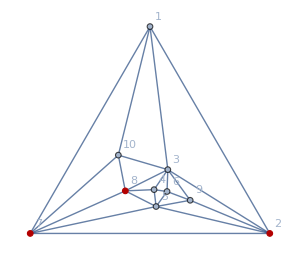

```mathematica
With [{g=ReadGrof[207]},
Graph[g,VertexLabels->"Name",GraphLayout->"TutteEmbedding", GraphHighlight->Select[VertexList[g],VertexDegree[g,#]==5&],ImageSize->300]
]
```

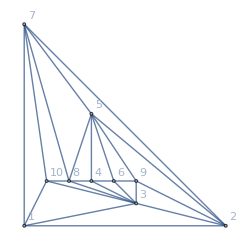
-Graphics-{(-3+x) (-2+x) (1271-2152 x+1551 x^2-613 x^3+141 x^4-18 x^5+x^6),168,True}
-Graphics-317380 | -Graphics-{-3+x,1,True} | -Graphics-{(-3+x)^4,1,True}
-Graphics-317140 | -Graphics-{-3+x,1,True} | -Graphics-{(-3+x) (-31+28 x-9 x^2+x^3),1,False}
-Graphics-317110 | -Graphics-{-4+x,0,False} | -Graphics-{94-115 x+55 x^2-12 x^3+x^4,2,False}
-Graphics-361660 | -Graphics-{-3+x,1,True} | -Graphics-{(-3+x)^2 (7-5 x+x^2),3,True}
-Graphics-296080 | -Graphics-{-3+x,1,True} | -Graphics-{(-3+x) (-22+22 x-8 x^2+x^3),2,False}
-Graphics-296050 | -Graphics-{-4+x,0,False} | -Graphics-{67-88 x+46 x^2-11 x^3+x^4,3,False}
-Graphics-361120 | -Graphics-{-3+x,1,True} | -Graphics-{(-4+x) (-3+x) (13-7 x+x^2),0,False}
-Graphics-360850 | -Graphics-{-4+x,0,False} | -Graphics-{(13-7 x+x^2)^2,1,False}
-Graphics-295510 | -Graphics-{-4+x,0,False} | -Graphics-{(-4+x)^2 (10-6 x+x^2),0,False}
-Graphics-295270 | -Graphics-{-4+x,0,False} | -Graphics-{(-4+x) (-43+35 x-10 x^2+x^3),0,False}
-Graphics-295240 | -Graphics-{-5+x,0,False} | -Graphics-{173-183 x+75 x^2-14 x^3+x^4,0,False}

```mathematica
WorkOnGraph2[ReadGrof[207],{7,5,4,3,10}]
```

```mathematica
WorkOnGraph2[ReadGrof[207],{2,3,6,5,7}]
```

-Graphics-{(-3+x) (-2+x) (1271-2152 x+1551 x^2-613 x^3+141 x^4-18 x^5+x^6),168,True}
-Graphics-361120 | -Graphics-{-3+x,1,True} | -Graphics-{(-3+x) (-22+22 x-8 x^2+x^3),2,False}
-Graphics-361660 | -Graphics-{-2+x,2,True} | -Graphics-{(-3+x) (-31+28 x-9 x^2+x^3),1,False}
-Graphics-360850 | -Graphics-{-3+x,1,True} | -Graphics-{(-4+x) (-43+35 x-10 x^2+x^3),0,False}
-Graphics-295510 | -Graphics-{-4+x,0,False} | -Graphics-{67-88 x+46 x^2-11 x^3+x^4,3,False}
-Graphics-296080 | -Graphics-{-3+x,1,True} | -Graphics-{(-3+x)^4,1,True}
-Graphics-296050 | -Graphics-{-3+x,1,True} | -Graphics-{94-115 x+55 x^2-12 x^3+x^4,2,False}
-Graphics-295270 | -Graphics-{-4+x,0,False} | -Graphics-{(-4+x)^2 (10-6 x+x^2),0,False}
-Graphics-295240 | -Graphics-{-4+x,0,False} | -Graphics-{173-183 x+75 x^2-14 x^3+x^4,0,False}